# Monte Carlo Simulation using Mathematica

I have used Monte Carlo Simulation for years, but I' ve always used other platforms that are more naturally suited to it (JMP, Matlab, R, even Excel). Mathematica is a tool that I have always used for more pure Mathematics - solving equations, etc. - and not for statistical modeling work. But there’s no reason that it couldn’t be used for Monte Carlo Simulations! It has all of the built in tools and the quick calculations for it.
So, below is my quick example of a Monte Carlo Simulation (of CPU temperatures for a computer - hence the Fan/NoFan temp rise over ambient factors.

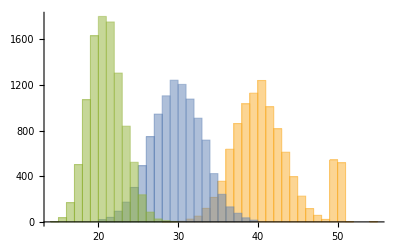

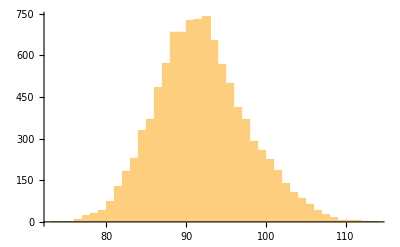

```mathematica
TempMean = 29.9;
TempStdDev = 3.2; 
LogMu = 0.2; 
LogSigma = 0.1; 
NoFanMean = 40;
NoFanStdDev=3;
FanMean=50; 
FanStdDev = 0.2;
SimulateNumber= 10000;
ThetaJAMu=17.1; ThetaJASigma=0.04;
AmbientTemp= RandomVariate[TruncatedDistribution[{20,40},NormalDistribution[TempMean,TempStdDev]],SimulateNumber];
ThermalFactor= RandomVariate[LogNormalDistribution[LogMu,LogSigma],SimulateNumber];
ThetaJA = RandomVariate[NormalDistribution[ThetaJAMu, ThetaJASigma], SimulateNumber];
TROA = RandomVariate[MixtureDistribution[{90,10},{NormalDistribution[NoFanMean,NoFanStdDev],NormalDistribution[FanMean,FanStdDev]}],SimulateNumber];
Temp1=AmbientTemp+ThetaJA*ThermalFactor+TROA;
Histogram[{TROA, AmbientTemp,ThermalFactor*ThetaJA},50]
Histogram[Temp1,50]
```